# Feynman’s clock based CCNOT

“What I cannot create, I do not understand”

http://www.quora.com/What-did-Richard-Feynman-mean-when-he-said-What-I-cannot-create-I-do-not-understand

## In principio era l’algebra di Spin 1/2....

Creiamo 3 matrici di Pauli e la matrice identità per operare su un singolo qubit. 
Lo spin è il momento angolare intrinseco di una particella, è un fenomeno totalmente quantistico. (Nel nostro caso stiamo parlando, di un elettrone fermo).
Se fissiamo una direzione nel nostro spazio (l’asse z) e misuriamo la componente dello spin sull’asse z, otterremo due soli valori: +1 e -1 (quasi..). Questa è la caratteristica dei sistemi a spin 1/2. 
Più esattamente, il sistema dello spin ha due soli stati, ovvero descrivibili con uno spazio di Hilbert a due dimensioni sul campo C. 
Il qubit è un vettore unitario in uno spazio di Hilbert a 2 dimensioni. Lo spazio che creiamo è fatto dagli autovettori della matrice σz moltiplicata per -1.
Le osservabili, ovvero sistemi fisici sui quali ha senso fare una misura in un sistema del genere sono 4: andiamoli a vedere.

```mathematica
Clear[uno,σx,σy, σz];
uno = IdentityMatrix[2]
{σx,σy, σz}=PauliMatrix[Range[3]];
σx//MatrixForm
σy//MatrixForm
σz//MatrixForm
```

{{1,0},{0,1}}

(0 | 1
1 | 0)

(0 | -ⅈ
ⅈ | 0)

(1 | 0
0 | -1)

...o meglio la sua variante in maniera da avere l’autovalore -1 corrispondente allo stato down e l’autovalore 1 corrispondente allo stato up.

```mathematica
Clear[σ3,σ1];
Exp[ⅈ π]==-1
σ3=Exp[ⅈ π]*σz
σ1=σx
σ3 // MatrixForm
σz // MatrixForm
```

True

{{-1,0},{0,1}}

{{0,1},{1,0}}

(-1 | 0
0 | 1)

(1 | 0
0 | -1)

Creiamo una funzione che ci dice quanto vale il commutatore tra due matrici:

```mathematica
Clear[commMatr];
commMatr[A_,B_]=A.B-B.A
```

A.B-B.A

Costruiamo  σ2 in modo tale che soddisfi le regole di commutazione canonica.

```mathematica
Clear[σ2];
σ2=1/(2 ⅈ) commMatr[σ3,σ1]
```

{{0,ⅈ},{-ⅈ,0}}

Verifichiamo le regole di commutazione canonica.

```mathematica
commMatr[σ1,σ2] == 2ⅈ σ3
commMatr[σ2,σ3] == 2ⅈ σ1
(*Questa per costruzione*)
commMatr[σ3,σ1] == 2 ⅈ σ2
```

True

True

True

Il commutatore ci dice che due diverse componenti dello spin non sono osservabili compatibili ovvero non possono essere misurate insieme.

## La base computazionale

Usiamo la direzione 3 (z) come direzione spaziale in cui codifichiamo l’informazione classica (bit).

Studiamo quindi l’operatore σ3, ovvero il suo spettro e i suoi autovettori.

```mathematica
Eigensystem[σ3]
```

{{-1,1},{{1,0},{0,1}}}

Diamo un nome proprio ai due autostati, giusto per migliorare la leggibilità del codice

```mathematica
Clear[up,down];
{down, up} = Eigensystem[σ3][[2]]
```

{{1,0},{0,1}}

```mathematica
down//TableForm
```

1
0

```mathematica
up //TableForm
```

0
1

Giusto per sicurezza, verifichiamo l’ovvio, ovvero che l’operatore di creazione e di annichilazione funzionino correttamente.

```mathematica
σ3.down ==  -1 down
σ3.up == 1 up
```

True

True

## Operatori di raising e lowering

```mathematica
Clear[banale];
banale={0,0}
```

{0,0}

```mathematica
Clear[σplus, σminus];
σplus=(σ1+ⅈ σ2)/2;
σminus=(σ1-ⅈ σ2)/2;
```

```mathematica
σplus//MatrixForm
σminus//MatrixForm
```

(0 | 0
1 | 0)

(0 | 1
0 | 0)

Vediamo che cosa fanno (e perché si chiamano così)...

```mathematica
σplus.up==banale
```

True

```mathematica
σplus.down==up
```

True

```mathematica
σminus.up==down
```

True

```mathematica
σminus.down==banale
```

True

Cosa fa la matrice σy? Aggiunge una “fase globale” al mio qubit.

```mathematica
up // MatrixForm
test=σy.up
```

(0
1)

{-ⅈ,0}

```mathematica
σ3.test // MatrixForm
```

(ⅈ
0)

```mathematica
σ3.test == -1 test
```

True

## Un paio di osservazioni

Verifichiamo che gli operatori su gli spin siano autoaggiunti.

```mathematica
σ1==ConjugateTranspose[σ1]
σ2==ConjugateTranspose[σ2]
σ3==ConjugateTranspose[σ3]
```

True

True

True

```mathematica
σ1.σ1 == uno
```

True

e quindi sono grandezze osservabili

```mathematica
Clear[vettProva];
vettProva={α,β};
```

Affinche` il vettore di prova sia interessante, deve avere norma 1, in maniera da soddisfare un postulato della meccanica quantistica. Proviamo a risolvere il problema:

```mathematica
Solve[Abs[α]^2+Abs[β]^2==1,β]
```

{{β→-√(1-Abs[α]^2)},{β→√(1-Abs[α]^2)}}

Esistono quindi 2 soluzioni che però differiscono di un fattore di fase (ⅈπ).
Prendiamo, per il momento la prima soluzione.

```mathematica
Clear[vettProva];
vettProva ={α,β}/.Solve[Abs[α]^2+Abs[β]^2==1,β][[1,1]]
```

{α,-√(1-Abs[α]^2)}

```mathematica
Manipulate[
{
Conjugate[vettProva].σ3.vettProva,
Conjugate[vettProva].σ1.vettProva,
Conjugate[vettProva].σ2.vettProva}/.α->c,{c,0,1,0.1}]
```

Qui ottengo i valori attesi delle tre osservabili <x|A|x> dove x è un versore unitario e A sono le 3 matrici di pauli. 
Faccio assumere al mio parametro α i valori che assume la variabile c. (che va da 0 a 1).
Vediamo per esempio, come con α=0 e b=1 il mio valore atteso di σ3 è 1!

## Passiamo a k-spin:

Cominciamo con il costruire l’algebra degli operatori per una collezione di k spin 1/2.

Si può dimostrare che l’algebra degli operatori per una collezione di sistemi di spin 1/2 è quella generata dal prodotto tensore delle algebre di singolo spin.
Qui sotto sono costruiti i generatori di tale algebra, ovvero delle funzioni che prendono come parametro il numero di elementi della nostra collezione, e l’elemento k-esimo della collezione alla quale applicare la matrice.

```mathematica
Clear[Σ1,Σ2,Σ3, Σ0];
Σ1[s_][k_]:=Σ1[s][k]=Block[{lista,appo,temp},
lista=ReplacePart[ConstantArray[uno, s], k-> σ1];

appo = lista[[1]];
For[i=2,i≤Length[lista],i++,
appo=KroneckerProduct[appo,lista[[i]]]
];
appo
]

Σ2[s_][k_]:=Σ2[s][k]=Block[{lista,appo,temp},
lista=ReplacePart[ConstantArray[uno, s], k-> σ2];

appo = lista[[1]];
For[i=2,i≤Length[lista],i++,
appo=KroneckerProduct[appo,lista[[i]]]
];
appo
]
Σ3[s_][k_]:=Σ3[s][k]=Block[{lista,appo,temp},
lista=ReplacePart[ConstantArray[uno, s], k-> σ3];

appo = lista[[1]];
For[i=2,i≤Length[lista],i++,
appo=KroneckerProduct[appo,lista[[i]]]
];
appo
]

Σ0[s_]:=Σ0[s]=Block[{lista,appo,temp},
	lista=ConstantArray[uno, s];

appo = lista[[1]];
For[i=2,i≤Length[lista],i++,
appo=KroneckerProduct[appo,lista[[i]]]
];
appo
]
```

Verifichiamo che gli operatori siano ben definiti.
Cominciamo con il vederne un paio per s=3

```mathematica
Clear[s];
s=3;
```

```mathematica
Table[Σ1[s][k]//MatrixForm,{k,1,s}]
```

{(0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0),(0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0)}

```mathematica
Table[Σ2[s][k]//MatrixForm,{k,1,s}]
```

{(0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ
-ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0),(0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0
-ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ
0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0),(0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0
-ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0
0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0
0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ
0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0)}

```mathematica
Table[Σ3[s][k]//MatrixForm,{k,1,s}]
```

{(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)}

Verifichiamo le regole di commutazione esattamente come per le matrici precedenti.

```mathematica
Clear[matbanale];
matbanale[s_]:=matbanale[s]=ConstantArray[0, {2^s,2^s}];
```

Gli operatori che agiscono sullo stesso spin seguono le regole di commutazione della sezione precedente

```mathematica
Table[commMatr[Σ1[s][k],Σ2[s][k]]==2ⅈ Σ3[s][k],{k,1,s}]
Table[commMatr[Σ2[s][k],Σ3[s][k]]==2ⅈ Σ1[s][k],{k,1,s}]
Table[commMatr[Σ3[s][k],Σ1[s][k]]==2ⅈ Σ2[s][k],{k,1,s}]
```

{True,True,True}

{True,True,True}

{True,True,True}

Operatori che agiscono su spin differenti commutano, cerchiamo di verificarlo compilando alcune tabelle.
Verifichiamo che quando gli indici j e k sono differenti le matrici commutano, ovvero il commutatore è la matrice banale.
Servono 3 tabelle distinte, in quanto abbiamo 3 possibili combinazioni per le matrici.3!(2!(3-2)!)
Due osservabili sono compatibili se gli operatori che le rappresentano commutano.

```mathematica
Table[commMatr[Σ1[s][k],Σ2[s][j]]==matbanale[s],{k,1,s},{j,1,s}]//MatrixForm
Table[commMatr[Σ2[s][k],Σ3[s][j]]==matbanale[s],{k,1,s},{j,1,s}]//MatrixForm
Table[commMatr[Σ3[s][k],Σ1[s][j]]==matbanale[s],{k,1,s},{j,1,s}]//MatrixForm
```

(False | True | True
True | False | True
True | True | False)

(False | True | True
True | False | True
True | True | False)

(False | True | True
True | False | True
True | True | False)

Vediamo come agiscono gli operatori sugli elementi (alcuni) della base computazionale.
Per due osservabili qualsiasi, abbiamo che
ΔAΔB  ≧ 1/2 * || [A,B] ||

## Una parentesi: costruzione della base computazionale.

Per determinare la base computazionale per una collezione di s qubit:
-Trovo prima l’insieme delle configurazioni possibili: {-1,+1}^s.
-Poi ordino l’insieme in ordine lessicografico, con -1 che precede +1.
-Poi, per ogni configurazione, assegno a ciascuna occorrenza del valore -1 lo stato down, al valore +1 lo stato up.
-Poi tensiorializzo.

Ecco la base computazionale.

```mathematica
Clear[findCompBasis];
findCompBasis[s_]:= findCompBasis[s] = Block[{range,appo,lista,prod,tabella},
range=Map[IntegerDigits[#,2,s]&,Range[0,2^s-1]];
appo=Table[ Reverse[Table[(1-range[[j,i]])*down+range[[j,i]]*up,{i,1,s}]],{j,1,Length[range]}];
tabella=Table[
Clear[lista];
lista=appo[[k]];
prod = lista[[1]];
For[i=2,i≤Length[lista],i++,
prod=Flatten[KroneckerProduct[prod,lista[[i]]]]
];
prod,{k,1,Length[appo]}];
{appo,tabella}
]
```

```mathematica
Abs[{-1,-1}]
```

{1,1}

Questa funzione serve esclusivamente per visualizzare lo stato del mio sistema di qubit. Ovvero per ogni elemento della base, mi ritorna lo stato dei miei qubit associata.

```mathematica
Clear[whichQ];
whichQ[s_][stato_]:=Block[{appo},
(*questo passaggio serve per il controllo degli operatori*)
appo=Abs[stato];
IntegerDigits[Position[appo,1][[1,1]]-1,2,s]]
```

la matrice “mappa” contiene tutte le possibili combinazioni dei miei qubit, espressi però come vettori della base computazionale.
la matrice baseComp invece contiene i vettori della mia base computazionale. Ovvero i vettori unitari di una base canonica.

```mathematica
Clear[mappa,baseComp];
{mappa,baseComp}=findCompBasis[s];
```

Qui per esempio, vediamo la base computazionale e le combinazioni dei qubit ad essa associati, per un sistema di 2 qubit.

```mathematica
findCompBasis[2] // MatrixForm
```

({{1,0},{1,0}} | {{0,1},{1,0}} | {{1,0},{0,1}} | {{0,1},{0,1}}
{1,0,0,0} | {0,0,1,0} | {0,1,0,0} | {0,0,0,1})

```mathematica
Table[whichQ[s][baseComp[[k]]],{k,1,Length[baseComp]}] // MatrixForm
```

(0 | 0 | 0
1 | 0 | 0
0 | 1 | 0
1 | 1 | 0
0 | 0 | 1
1 | 0 | 1
0 | 1 | 1
1 | 1 | 1)

Questa tabella ci mostra che effettivamente abbiamo ottenuto tutte le possibili combinazioni di 3 qubit.

Ovviamente avremmo potuto ottenere lo stesso risultato prendendo 2^s vettori di zeri e settando a uno un solo elemento di ciascun vettore....ma sarebbe stato meno divertente.

## Verifichiamo l’azione degli operatori sui vettori di base

```mathematica
Table[
{m,whichQ[s][baseComp[[k]]],res=Σ1[s][m].baseComp[[k]];whichQ[s][res]},{m,1,s},{k,1,Length[baseComp]}]  // MatrixForm
```

((1
{0,0,0}
{1,0,0}) | (1
{1,0,0}
{0,0,0}) | (1
{0,1,0}
{1,1,0}) | (1
{1,1,0}
{0,1,0}) | (1
{0,0,1}
{1,0,1}) | (1
{1,0,1}
{0,0,1}) | (1
{0,1,1}
{1,1,1}) | (1
{1,1,1}
{0,1,1})
(2
{0,0,0}
{0,1,0}) | (2
{1,0,0}
{1,1,0}) | (2
{0,1,0}
{0,0,0}) | (2
{1,1,0}
{1,0,0}) | (2
{0,0,1}
{0,1,1}) | (2
{1,0,1}
{1,1,1}) | (2
{0,1,1}
{0,0,1}) | (2
{1,1,1}
{1,0,1})
(3
{0,0,0}
{0,0,1}) | (3
{1,0,0}
{1,0,1}) | (3
{0,1,0}
{0,1,1}) | (3
{1,1,0}
{1,1,1}) | (3
{0,0,1}
{0,0,0}) | (3
{1,0,1}
{1,0,0}) | (3
{0,1,1}
{0,1,0}) | (3
{1,1,1}
{1,1,0}))

```mathematica
Table[
{m,whichQ[s][baseComp[[k]]],res=Σ3[s][m].baseComp[[k]];whichQ[s][res]},{m,1,s},{k,1,Length[baseComp]}] // MatrixForm
```

((1
{0,0,0}
{0,0,0}) | (1
{1,0,0}
{1,0,0}) | (1
{0,1,0}
{0,1,0}) | (1
{1,1,0}
{1,1,0}) | (1
{0,0,1}
{0,0,1}) | (1
{1,0,1}
{1,0,1}) | (1
{0,1,1}
{0,1,1}) | (1
{1,1,1}
{1,1,1})
(2
{0,0,0}
{0,0,0}) | (2
{1,0,0}
{1,0,0}) | (2
{0,1,0}
{0,1,0}) | (2
{1,1,0}
{1,1,0}) | (2
{0,0,1}
{0,0,1}) | (2
{1,0,1}
{1,0,1}) | (2
{0,1,1}
{0,1,1}) | (2
{1,1,1}
{1,1,1})
(3
{0,0,0}
{0,0,0}) | (3
{1,0,0}
{1,0,0}) | (3
{0,1,0}
{0,1,0}) | (3
{1,1,0}
{1,1,0}) | (3
{0,0,1}
{0,0,1}) | (3
{1,0,1}
{1,0,1}) | (3
{0,1,1}
{0,1,1}) | (3
{1,1,1}
{1,1,1}))

```mathematica
(*Questo controllo ha poco senso....praticamente e` equivalente a quello per Σ1 per come e` definita
la funzione whichQ...*)
Table[
{m,whichQ[s][baseComp[[k]]],res=Σ2[s][m].baseComp[[k]];whichQ[s][res]},{m,1,s},{k,1,Length[baseComp]}] // MatrixForm
```

((1
{0,0,0}
{1,0,0}) | (1
{1,0,0}
{0,0,0}) | (1
{0,1,0}
{1,1,0}) | (1
{1,1,0}
{0,1,0}) | (1
{0,0,1}
{1,0,1}) | (1
{1,0,1}
{0,0,1}) | (1
{0,1,1}
{1,1,1}) | (1
{1,1,1}
{0,1,1})
(2
{0,0,0}
{0,1,0}) | (2
{1,0,0}
{1,1,0}) | (2
{0,1,0}
{0,0,0}) | (2
{1,1,0}
{1,0,0}) | (2
{0,0,1}
{0,1,1}) | (2
{1,0,1}
{1,1,1}) | (2
{0,1,1}
{0,0,1}) | (2
{1,1,1}
{1,0,1})
(3
{0,0,0}
{0,0,1}) | (3
{1,0,0}
{1,0,1}) | (3
{0,1,0}
{0,1,1}) | (3
{1,1,0}
{1,1,1}) | (3
{0,0,1}
{0,0,0}) | (3
{1,0,1}
{1,0,0}) | (3
{0,1,1}
{0,1,0}) | (3
{1,1,1}
{1,1,0}))

```mathematica
Table[{m,whichQ[s][baseComp⟦k⟧],res=Σ0[s].baseComp⟦k⟧;whichQ[s][res]},{m,1,s},{k,1,Length[baseComp]}] // MatrixForm
```

((1
{0,0,0}
{0,0,0}) | (1
{1,0,0}
{1,0,0}) | (1
{0,1,0}
{0,1,0}) | (1
{1,1,0}
{1,1,0}) | (1
{0,0,1}
{0,0,1}) | (1
{1,0,1}
{1,0,1}) | (1
{0,1,1}
{0,1,1}) | (1
{1,1,1}
{1,1,1})
(2
{0,0,0}
{0,0,0}) | (2
{1,0,0}
{1,0,0}) | (2
{0,1,0}
{0,1,0}) | (2
{1,1,0}
{1,1,0}) | (2
{0,0,1}
{0,0,1}) | (2
{1,0,1}
{1,0,1}) | (2
{0,1,1}
{0,1,1}) | (2
{1,1,1}
{1,1,1})
(3
{0,0,0}
{0,0,0}) | (3
{1,0,0}
{1,0,0}) | (3
{0,1,0}
{0,1,0}) | (3
{1,1,0}
{1,1,0}) | (3
{0,0,1}
{0,0,1}) | (3
{1,0,1}
{1,0,1}) | (3
{0,1,1}
{0,1,1}) | (3
{1,1,1}
{1,1,1}))

## Operatori Σplus e Σminus

Qua li definisco mediante tensorializzazione di  σ1,2,3

```mathematica
Clear[Σplus, Σminus]
(* Definiamoli in maniera esplicita, con il prodotto tensore *)
Σplus[s_][k_]:=Σplus[s][k]=Block[{lista,appo},
lista=ReplacePart[ConstantArray[uno, s], k-> σplus];
appo = lista[[1]];
For[i=2,i≤Length[lista],i++,
appo=KroneckerProduct[appo,lista[[i]]]
];
appo
]
Σminus[s_][k_]:=Σminus[s][k]=Block[{lista,appo},
lista=ReplacePart[ConstantArray[uno, s], k-> σminus];
appo = lista[[1]];
For[i=2,i≤Length[lista],i++,
appo=KroneckerProduct[appo,lista[[i]]]
];
appo
]
```

Qua invece li ridefinisco in maniera diversa, magari più elegante (in modo da evitare errori...)

```mathematica
Clear[Σplus2, Σminus2]
Σplus2[s_][k_]:=Σplus2[s][k]= (Σ1[s][k]+ⅈ*Σ2[s][k])/2
Σminus2[s_][k_]:= Σminus2[s][k]=(Σ1[s][k]-ⅈ*Σ2[s][k])/2
Table[commMatr[Σminus2[s][k],Σminus[s][k]]==matbanale[s],{k,1,s}]//MatrixForm
Table[commMatr[Σplus2[s][k],Σplus[s][k]]==matbanale[s],{k,1,s}]//MatrixForm
```

(True
True
True)

(True
True
True)

Ho appena verificato che le due matrici così definite siano uguali.

Vediamo un’esempio di queste matrici:

```mathematica
Table[Σplus[s][k]//MatrixForm,{k,1,s}]
Table[Σminus[s][k]//MatrixForm,{k,1,s}]
```

{(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0)}

{(0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)}

### Verifico che le matrici che “accendono” e “spengono” un qubit funzionino:

Questa matrice crea l’eccitazione sul qubit k. Verifichiamo cosa succede per ogni configurazione possibile del nostro sistema.

```mathematica
Table[
{m,whichQ[s][baseComp[[k]]],res=Σplus[s][m].baseComp[[k]];whichQ[s][res]},{m,1,s},{k,1,Length[baseComp]}] // MatrixForm
```

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

((1
{0,0,0}
{1,0,0}) | (1
{1,0,0}
IntegerDigits[-1+{}⟦1,1⟧,2,3]) | (1
{0,1,0}
{1,1,0}) | (1
{1,1,0}
IntegerDigits[-1+{}⟦1,1⟧,2,3]) | (1
{0,0,1}
{1,0,1}) | (1
{1,0,1}
IntegerDigits[-1+{}⟦1,1⟧,2,3]) | (1
{0,1,1}
{1,1,1}) | (1
{1,1,1}
IntegerDigits[-1+{}⟦1,1⟧,2,3])
(2
{0,0,0}
{0,1,0}) | (2
{1,0,0}
{1,1,0}) | (2
{0,1,0}
IntegerDigits[-1+{}⟦1,1⟧,2,3]) | (2
{1,1,0}
IntegerDigits[-1+{}⟦1,1⟧,2,3]) | (2
{0,0,1}
{0,1,1}) | (2
{1,0,1}
{1,1,1}) | (2
{0,1,1}
IntegerDigits[-1+{}⟦1,1⟧,2,3]) | (2
{1,1,1}
IntegerDigits[-1+{}⟦1,1⟧,2,3])
(3
{0,0,0}
{0,0,1}) | (3
{1,0,0}
{1,0,1}) | (3
{0,1,0}
{0,1,1}) | (3
{1,1,0}
{1,1,1}) | (3
{0,0,1}
IntegerDigits[-1+{}⟦1,1⟧,2,3]) | (3
{1,0,1}
IntegerDigits[-1+{}⟦1,1⟧,2,3]) | (3
{0,1,1}
IntegerDigits[-1+{}⟦1,1⟧,2,3]) | (3
{1,1,1}
IntegerDigits[-1+{}⟦1,1⟧,2,3]))

```mathematica
Table[
{m,whichQ[s][baseComp[[k]]],res=Σminus[s][m].baseComp[[k]];whichQ[s][res]},{m,1,s},{k,1,Length[baseComp]}] // MatrixForm
```

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

((1
{0,0,0}
IntegerDigits[-1+{}⟦1,1⟧,2,3]) | (1
{1,0,0}
{0,0,0}) | (1
{0,1,0}
IntegerDigits[-1+{}⟦1,1⟧,2,3]) | (1
{1,1,0}
{0,1,0}) | (1
{0,0,1}
IntegerDigits[-1+{}⟦1,1⟧,2,3]) | (1
{1,0,1}
{0,0,1}) | (1
{0,1,1}
IntegerDigits[-1+{}⟦1,1⟧,2,3]) | (1
{1,1,1}
{0,1,1})
(2
{0,0,0}
IntegerDigits[-1+{}⟦1,1⟧,2,3]) | (2
{1,0,0}
IntegerDigits[-1+{}⟦1,1⟧,2,3]) | (2
{0,1,0}
{0,0,0}) | (2
{1,1,0}
{1,0,0}) | (2
{0,0,1}
IntegerDigits[-1+{}⟦1,1⟧,2,3]) | (2
{1,0,1}
IntegerDigits[-1+{}⟦1,1⟧,2,3]) | (2
{0,1,1}
{0,0,1}) | (2
{1,1,1}
{1,0,1})
(3
{0,0,0}
IntegerDigits[-1+{}⟦1,1⟧,2,3]) | (3
{1,0,0}
IntegerDigits[-1+{}⟦1,1⟧,2,3]) | (3
{0,1,0}
IntegerDigits[-1+{}⟦1,1⟧,2,3]) | (3
{1,1,0}
IntegerDigits[-1+{}⟦1,1⟧,2,3]) | (3
{0,0,1}
{0,0,0}) | (3
{1,0,1}
{1,0,0}) | (3
{0,1,1}
{0,1,0}) | (3
{1,1,1}
{1,1,0}))

General::stop: Further output of Part :: partw will be suppressed during this calculation.

# Creo la matrice che sposta la mia eccitazione da un qubit al successivo

Questa matrice può essere creata per spostare un’eccitazione dal qubit k al qubit j, mantenendo invariato il numero di qubit totali su tutta la mia catena.

```mathematica
Sposta[s_][k_]:=Sposta[s][k]=Σplus[s][k].Σminus[s][k-1]
Table[
{m,whichQ[s][baseComp[[k]]],res=Sposta[s][m].baseComp[[k]];whichQ[s][res]},{m,1,s},{k,1,Length[baseComp]}] // MatrixForm
```

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

((1
{0,0,0}
{1,0,0}) | (1
{1,0,0}
IntegerDigits[-1+{}⟦1,1⟧,2,3]) | (1
{0,1,0}
{1,1,0}) | (1
{1,1,0}
IntegerDigits[-1+{}⟦1,1⟧,2,3]) | (1
{0,0,1}
{1,0,1}) | (1
{1,0,1}
IntegerDigits[-1+{}⟦1,1⟧,2,3]) | (1
{0,1,1}
{1,1,1}) | (1
{1,1,1}
IntegerDigits[-1+{}⟦1,1⟧,2,3])
(2
{0,0,0}
IntegerDigits[-1+{}⟦1,1⟧,2,3]) | (2
{1,0,0}
{0,1,0}) | (2
{0,1,0}
IntegerDigits[-1+{}⟦1,1⟧,2,3]) | (2
{1,1,0}
IntegerDigits[-1+{}⟦1,1⟧,2,3]) | (2
{0,0,1}
IntegerDigits[-1+{}⟦1,1⟧,2,3]) | (2
{1,0,1}
{0,1,1}) | (2
{0,1,1}
IntegerDigits[-1+{}⟦1,1⟧,2,3]) | (2
{1,1,1}
IntegerDigits[-1+{}⟦1,1⟧,2,3])
(3
{0,0,0}
IntegerDigits[-1+{}⟦1,1⟧,2,3]) | (3
{1,0,0}
IntegerDigits[-1+{}⟦1,1⟧,2,3]) | (3
{0,1,0}
{0,0,1}) | (3
{1,1,0}
{1,0,1}) | (3
{0,0,1}
IntegerDigits[-1+{}⟦1,1⟧,2,3]) | (3
{1,0,1}
IntegerDigits[-1+{}⟦1,1⟧,2,3]) | (3
{0,1,1}
IntegerDigits[-1+{}⟦1,1⟧,2,3]) | (3
{1,1,1}
IntegerDigits[-1+{}⟦1,1⟧,2,3]))

## Regole di commutazione su matrici Σplus e minus

```mathematica
Table[commMatr[Σ3[s][j],Σplus[s][j]]==  2 Σplus[s][j],{j,1,s}]//MatrixForm
Table[commMatr[Σplus[s][j],Σminus[s][j]]==  Σ3[s][j],{j,1,s}]//MatrixForm
Table[Σplus[s][j].Σminus[s][j] - Σminus[s][j].Σplus[s][j]  == Σ3[s][j], {j,1,s}]// MatrixForm
```

(True
True
True)

(True
True
True)

(True
True
True)

## Riduzione dimensionale del clock

Sfruttando il fatto che l’eccitazione sulla mia catena del cursore rappresenta un’invariante del moto, so che mi muovo in un sottospazio proprio di tutte le possibili combinazioni. 
Posso così ridurre la dimensione del mio spazio totale del cursore, alle sole combinazioni con solo uno spin-up. 
Devo quindi ricrearmi un’algebra che mi permetta di muovermi in un sottospazio proprio, senza la possibilità di uscirne.

Definisco i miei stati up e down.

```mathematica
upr=1;
downr=-1;
```

La lunghezza della mia catena di spin (ridotta)

```mathematica
Clear[r]
r=12;
```

```mathematica
Clear[baseVector]
baseVector[s_][pos_]:= baseVector[s][pos] = Return[ReplacePart[ConstantArray[0, s], pos -> upr]]
```

### Definisco una “nuova” σ3r e ne verifico il comportamento

```mathematica
Clear[σ3r]
σ3r[s_][p_] := σ3r[s][p] = Block[{appo}, 
appo= ReplacePart[ConstantArray[downr, s], p -> 1] ;
 DiagonalMatrix[appo]
];
σ3r[r][3] //MatrixForm
σ3r[r][3].baseVector[r][3]
```

(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1)

{0,0,1,0,0,0,0,0,0,0,0,0}

Anche in questo caso, σ3 mi “porta fuori” dal mio vettore un segno.

```mathematica
Table[σ3r[6][k]//MatrixForm,{k,1,6}]
```

{(1 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | -1),(-1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | -1),(-1 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | -1),(-1 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | -1),(-1 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | -1),(-1 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 1)}

### Operatori “destra” e “sinistra” |k><k-1| + c.c

```mathematica
Clear[bra,ket]
bra[s_][p_] := bra[s][p] = baseVector[s][p]
ket[s_][p_] := ket[s][p] = Transpose[Conjugate[{baseVector[s][p]}]]

(*Muove a destra il cursore DALLA posizione corente p_*)
Clear[moveRight,moveLeft]
moveRight[s_][p_] := moveRight[s][p] = KroneckerProduct[ket[s][p+1],bra[s][p]]
moveLeft[s_][p_] := moveLeft[s][p] =KroneckerProduct[ket[s][p],bra[s][p+1]]

moveRight[r][1] // MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

Attenzione: questo operatore non è autoaggiunto, e devo aggiungere “a mano” ogni volta il suo complesso coniugato

```mathematica
Clear[moveToFrom]
moveToFrom[s_][to_][from_] := moveToFrom[s][to][from] = KroneckerProduct[ket[s][to],bra[s][from]]
moveToFrom[r][2][1] // MatrixForm
baseVector[r][1]
baseVector[r][2]
moveToFrom[r][2][1].baseVector[r][1]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

{1,0,0,0,0,0,0,0,0,0,0,0}

{0,1,0,0,0,0,0,0,0,0,0,0}

Questo è l’operatore autoaggiunto invece

```mathematica
Clear[moveGeneric]
moveGeneric[s_][to_][from_] := moveGeneric[s][to][from] = KroneckerProduct[ket[s][to],bra[s][from]]+ConjugateTranspose[ KroneckerProduct[ket[s][to],bra[s][from]]]
moveGeneric[r][2][1] // MatrixForm
```

(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

### Creo l’Hamiltoniano del cursore

Moltiplico tutto per -1/2 perchè faccio un “rescaling” delle energie per semplificarmi i calcoli. 
L’hamiltoniana è una matrice autoaggiunta (ovver hermitiana) ovvero A=TransposeConjugate[A].

```mathematica
Clear[H]
H= ConstantArray[0, {r,r}];
H=-1/2 Sum[moveRight[r][i]+moveLeft[r][i], {i, r-1}];
H // MatrixForm
```

(0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1/2 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1/2 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1/2 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1/2 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1/2 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1/2 | 0 | -1/2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | -1/2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | -1/2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | -1/2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | -1/2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0)

```mathematica
commMatr[ H, Sum[σ3r[r][k], {k,1,r}] // N] // MatrixForm
```

(0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.)

Verifico che mi sposti l’eccitazione correttamente

```mathematica
H.baseVector[r][2]
```

{-1/2,0,-1/2,0,0,0,0,0,0,0,0,0}

```mathematica
Manipulate[ListPlot[Abs[MatrixExp[-ⅈ H t // N].baseVector[r][1]]^2,Joined->True,
PlotRange->{0,1}],{t,0,100}]
```

Questo grafico rappresenta la probabilità di osservare l’eccitazione sul mio cursore ad una determinato tempo di esecuzione t. E’ importante osservare come la probabilità dipenda, data una matrice, dal tempo e dalla condizione iniziale.

```mathematica
Manipulate[ListPlot[Abs[MatrixExp[-ⅈ H t // N].baseVector[r][6]]^2,Joined->True,
PlotRange->{0,1}],{t,0,100}]
```

## Diagonalizzazione della matrice per miglioramento performance di esecuzione

Diagonalizzo la mia Hamiltoniana, trovando gli autovalori ed autovettori che mi determinino una nuova base dello spazio.

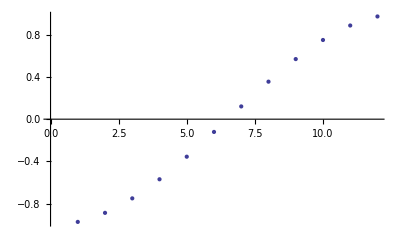

```mathematica
Clear[autoValH,autoVettH];
{autoValH,autoVettH}=Eigensystem[H//N];
ListPlot[Sort[autoValH]]
```

Verifico che i miei autovettori abbiano tutti norma2 uguale ad 1

```mathematica
Map[Norm[#,2]&,autoVettH]
```

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

Verifico quella che è la “risuluzione dell’identità” ovvero che la somma dei miei proiettori dia la matrice identità. Chop serve per compensare l’errore macchina.

```mathematica
Table[autoVettH[[k]].autoVettH[[h]],{h,1,r},{k,1,r}]//Chop//MatrixForm
```

(1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.)

Compongo creo le proiezioni della mia vecchia base sullo spazio generato da gli autovettori.

```mathematica
Clear[proiezioniNuovaBaseClock,proiezioniNuovaBaseClockTmp]
proiezioniNuovaBaseClockTmp=Table[Conjugate[autoVettH[[k]].baseVector[r][j]],{k,1,r}, {j,1,r}];
proiezioniNuovaBaseClock=Transpose[proiezioniNuovaBaseClockTmp];
```

In questo modo ho proiezioniNuovaBaseClock[statoPartenza][vettoreNuovaBase]

Definiamo il nostro stato evoluto.

```mathematica
Clear[evoluto];
evoluto[t_]:=Sum[Exp[-ⅈ t autoValH[[k]]]*proiezioniNuovaBaseClock[[1]][[k]]*autoVettH[[k]],{k,1,r}]//Chop
Manipulate[evoluto[t],{t,0,100}]
```

Questo grafico mi mostra come evolve il cursore fino tempo 100. Lo stato di partenza è il vettore di base con l’eccitazione in posizione 1.
Ci sono due grafici, che sono sovrapposti. Uno  dell’evoluzione con matrixExp e l’altro con Exp, ovvero quello che sfrutta la diagonalizzazione della matrice H.

```mathematica
Manipulate[ListPlot[{Abs[evoluto[t]]^2,Abs[MatrixExp[-ⅈ H t // N].baseVector[r][1]]^2},Joined->True,PlotRange->{0,1}],{t,0,100}]
```

```mathematica
Map[Norm[#,2]&,proiezioniNuovaBaseClock]
```

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

## La matrice C^uNOT.

#### CNOT

```mathematica
Clear[t];
t=2;
Clear[Cnot]
Cnot[s_][k_] := Cnot[s][k]=Σ0[s]+(Σ1[s][2]−Σ0[s] ).( (Σ0[s]+Σ3[s][1])/2)
Cnot[t][2] // MatrixForm
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0)

#### C^uNOT’s Matrix

```mathematica
Clear[t];
t=3;
Clear[CnotRep]
CnotRep[s_][contr_][k_] := Cnot[s][k]=Σ0[s]+(Σ1[s][k]−Σ0[s] ). Product[( (Σ0[s]+Σ3[s][contr[[i]]])/2), {i, 1, Length[contr]}]
(* Va passata una lista su quali sono i qubit di controllo *)
CnotRep[t][{1,2}][3] // MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0)

## Creazione del CNOT

#### Creo l’Hamiltoniano del CNOT

```mathematica
Clear[CNOTH]
CNOTH =
  -1/2 (
    KroneckerProduct[Σminus[2][1], moveToFrom[6][2][1]] + 
     Conjugate[Transpose[KroneckerProduct[Σminus[2][1], moveToFrom[6][2][1]]]] +
     KroneckerProduct[Σ1[2][2], moveToFrom[6][3][2]] +
     Conjugate[Transpose[KroneckerProduct[Σ1[2][2], moveToFrom[6][3][2]]]] +
     KroneckerProduct[Σplus[2][1], moveToFrom[6][6][3]] +
     Conjugate[Transpose[KroneckerProduct[Σplus[2][1], moveToFrom[6][6][3]]]] +
     KroneckerProduct[Σplus[2][1], moveToFrom[6][4][1]] +
     Conjugate[Transpose[KroneckerProduct[Σplus[2][1], moveToFrom[6][4][1]]]] +
     KroneckerProduct[Σ0[2], moveToFrom[6][5][4]] +
     Conjugate[Transpose[KroneckerProduct[Σ0[2], moveToFrom[6][5][4]]]] +
     KroneckerProduct[Σminus[2][1], moveToFrom[6][6][5]] +
     Conjugate[Transpose[KroneckerProduct[Σminus[2][1], moveToFrom[6][6][5]]]]);
```

Verifico che le dimensioni siano (2^2* 6)x(2^2* 6) = 24x24

```mathematica
Dimensions[CNOTH]
```

{24,24}

Creo i miei autovalori ed autovettori della matrice, verifico che abbiamo norma euclidea = 1 e che la somma dei proiettori dia la matrice identità.

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

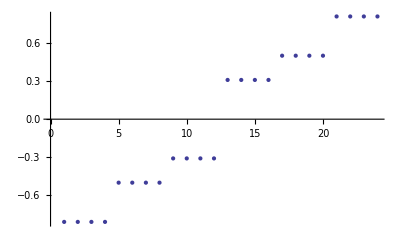

```mathematica
{CNOTHval, CNOTHvec}= Chop[Eigensystem[N[CNOTH]]] ;
Map[Norm[#,2]&,CNOTHvec]
ListPlot[Sort[CNOTHval]]
```

Ora verifico che tutti i miei autovettori siano tra loro ortonormali.
(Ma lo sapevo già: Un endomorfismo simmetrico rappresentato da una matrice su una base ortonormale (come quella canonica da me utilizzata), ha autovalori che formano una base ortonormale per lo spazio) .

```mathematica
Table[CNOTHvec[[k]].CNOTHvec[[h]],{h,1,Length[CNOTHvec]},{k,1,Length[CNOTHvec]}]//Chop//MatrixForm
```

(1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.)

### Creo stato iniziale e stato finale.

Il vettore iniziale è ottenuto tensorializzando il mio stato di partenza |1,1> del registro con lo stato |1> del clock (ridotto)
Lo stato scomposto è ottenuto proiettando il vettore di partenza su tute le componenti della nuova base diagonalizzata
Lo stato finale che mi aspetto di vedere è invece |1,0> tensorializzato con lo stato |6> del cursore.

```mathematica
Clear[rcnot,s, mappa2, baseComp2, startStateCNOT, scompoStartStateCNOT, finalStateCNOT]
rcnot=6;
s=2;
{mappa2,baseComp2}=findCompBasis[2];
whichQ[s][baseComp2[[4]]]
baseVector[rcnot][1]
```

{1,1}

{1,0,0,0,0,0}

```mathematica
startStateCNOT=Flatten[Outer[Times,baseComp2[[4]], baseVector[rcnot][1]]]
scompoStartStateCNOT=Table[Conjugate[CNOTHvec[[k]].startStateCNOT],{k,1,Length[CNOTHvec]}]

finalStateCNOT=Flatten[Outer[Times,baseComp2[[2]], baseVector[rcnot][6]]]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0}

{0.,0.,0.371748,0.,0.,0.,0.371748,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.601501,0.,0.,0.,0.,-0.601501,0.}

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0}

Verifico di aver fatto vettori unitari

```mathematica
Norm[startStateCNOT,2] == 1 && Norm[scompoStartStateCNOT,2] == 1 && Norm[finalStateCNOT,2] == 1
```

True

### Esempio di esecuzione del CNOT

#### Senza diagonalizzazione

```mathematica
Clear[evolutoCNOT];
evolutoCNOT[t_]:=MatrixExp[-ⅈ t CNOTH // N].startStateCNOT
Manipulate[evolutoCNOT[t],{t,0,100}]
```

Questa tabella ci mostra le ampiezze di probabilità del nostro vettore. 
Questo altro grafico invece ci mostra il valore atteso dell’eccitazione su tutti i miei qubit nel tempo. Osserviamo come, a causa del nostro stato iniziale, i qubit 4 e 5 non saranno mai eccitati.

```mathematica
Manipulate[ListPlot[1/2 (1+Table[Conjugate[evolutoCNOT[t]].KroneckerProduct[Σ0[2],
σ3r[6][k]].evolutoCNOT[t], {k,1,6}] // Chop), Joined -> True], {t,0,100}]
```

```mathematica
Manipulate[Conjugate[evolutoCNOT[t]].KroneckerProduct[Σ3[2][2],IdentityMatrix[6]].evolutoCNOT[t],{t,0,7.1}]
```

Verifichiamo che la somma totale delle probabilità sia sempre 1

```mathematica
Clear[SumTOT]
SumTOT[t_] := SumTOT[t] =Block[{next,appo},
next=evolutoCNOT[t];
Return[Norm[next,2]];
];
Manipulate[SumTOT[t], {t,0,100}]
```

#### Eseguiamo l’evoluzione del sistema con la matrice diagonalizzata del CNOT

```mathematica
Clear[evolutoCNOTD]
evolutoCNOTD[t_]:=Sum[Exp[-ⅈ t CNOTHval[[k]]]*scompoStartStateCNOT[[k]]*CNOTHvec[[k]],{k,1,Length[CNOTHvec]}]//Chop

Manipulate[evolutoCNOTD[t],{t,0,100}]
```

```mathematica
Clear[ SumTOTD]
SumTOTD[t_] := SumTOT[t] =Block[{next,appo},
next=evolutoCNOT[t];
Return[Norm[next,2]];
];
Manipulate[SumTOTD[t], {t,0,100}]
```

#### Verifico graficamente che i due risultati siano uguali, e che riesca a raggiungere il mio stato finale.

```mathematica
Needs["PlotLegends`"]
Manipulate[ListPlot[{Abs[evolutoCNOT[t]]^2, Abs[evolutoCNOTD[t]]^2, Abs[finalStateCNOT]^2}, 
GridLines->Automatic,  Joined->True, PlotRange->{0,1}],{t,0,50}]
```

Teorema Spettrale:
Ci dice una condizione necessaria e sufficiente per cui un endomorfismo (un’applicazione lineare tra uno spazio vettoriale e se stesso) è simmetrico.
Sia f un endomorfismo di V. f è simmetrico (e quindi si può diagonalizzare) sse f ammette una base ortonormale formata da autovettori di f.
Ovvero: essendo la mia matrice simmetrica rispetto alla base computazionale (che è un base canonica) posso dire che l’endomorfismo è simmetrico e quindi i suoi autovettori formano una nuova base ortonormale.

## Creazione del CCNOT

### Creo l’Hamiltoniano del CCNOT

```mathematica
Clear[r,s]
r=12;
s=3;
Clear[CCNOTH]
CCNOTH=
-1/2 (KroneckerProduct[Σminus[3][1],moveToFrom[12][2][1]]+ Conjugate[Transpose[KroneckerProduct[Σminus[3][1],moveToFrom[12][2][1]]]]+
KroneckerProduct[Σminus[3][2],moveToFrom[12][3][2]]+Conjugate[Transpose[KroneckerProduct[Σminus[3][2],moveToFrom[12][3][2]]]]+
KroneckerProduct[Σ1[3][3],moveToFrom[12][4][3]]+Conjugate[Transpose[KroneckerProduct[Σ1[3][3],moveToFrom[12][4][3]]]]+
KroneckerProduct[Σplus[3][2],moveToFrom[12][7][4]]+Conjugate[Transpose[KroneckerProduct[Σplus[3][2],moveToFrom[12][7][4]]]]+
KroneckerProduct[Σplus[3][1],moveToFrom[12][12][7]]+Conjugate[Transpose[KroneckerProduct[Σplus[3][1],moveToFrom[12][12][7]]]]+
KroneckerProduct[Σplus[3][2],moveToFrom[12][5][2]]+Conjugate[Transpose[KroneckerProduct[Σplus[3][2],moveToFrom[12][5][2]]]]+
KroneckerProduct[Σ0[3],moveToFrom[12][6][5]] +Conjugate[Transpose[KroneckerProduct[Σ0[3],moveToFrom[12][6][5]]] ]+
KroneckerProduct[Σminus[3][2],moveToFrom[12][7][6]]+Conjugate[Transpose[KroneckerProduct[Σminus[3][2],moveToFrom[12][7][6]]]]+
KroneckerProduct[Σplus[3][1],moveToFrom[12][8][1]]+Conjugate[Transpose[KroneckerProduct[Σplus[3][1],moveToFrom[12][8][1]]]]+
KroneckerProduct[Σ0[3],moveToFrom[12][9][8]]+Conjugate[Transpose[KroneckerProduct[Σ0[3],moveToFrom[12][9][8]]]]+
KroneckerProduct[Σ0[3],moveToFrom[12][10][9]]+Conjugate[Transpose[KroneckerProduct[Σ0[3],moveToFrom[12][10][9]]]]+
KroneckerProduct[Σ0[3],moveToFrom[12][11][10]]+Conjugate[Transpose[KroneckerProduct[Σ0[3],moveToFrom[12][11][10]]]]+
KroneckerProduct[Σminus[3][1],moveToFrom[12][12][11]]+Conjugate[Transpose[KroneckerProduct[Σminus[3][1],moveToFrom[12][12][11]]]]);
```

Verifico che le dimensioni siano (2^3* 12)x(2^3* 12) = 96x96

```mathematica
Dimensions[CCNOTH]
```

{96,96}

Creo i miei autovalori ed autovettori della matrice, verifico che abbiamo norma2 = 1 e che la somma dei proiettori dia la matrice identità.

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

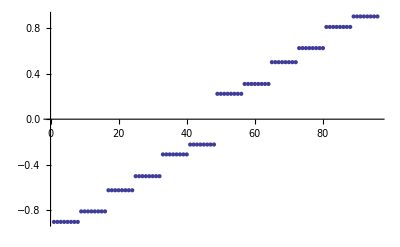

```mathematica
{CCNOTHval, CCNOTHvec}= Chop[Eigensystem[N[CCNOTH]]] ;
Map[Norm[#,2]&,CCNOTHvec]
ListPlot[Sort[CCNOTHval]]
```

Sopprimiamo l’output successvo a causa di motivi di leggibilità.

```mathematica
Table[CCNOTHvec[[k]].CCNOTHvec[[h]],{h,1,Length[CCNOTHvec]},{k,1,Length[CCNOTHvec]}];
```

#### Creo stato iniziale e stato finale.

Il vettore iniziale è ottenuto tensorializzando il mio stato di partenza |1,1,0> del registro con lo stato |1> del clock (ridotto)
Lo stato scomposto è ottenuto proiettando il vettore di partenza su tute le componenti della nuova base diagonalizzata
Lo stato finale è ottenuto tensorializzando |1,1,1> con |12>

```mathematica
Clear[rcnot,s, mappa3, baseComp3, startState, scompoStartState, finalState, scompoFinalState]
rcnot=12;
s=3;
{mappa3,baseComp3}=findCompBasis[s];
```

```mathematica
whichQ[s][baseComp3[[4]]]
baseVector[r][1]
```

{1,1,0}

{1,0,0,0,0,0,0,0,0,0,0,0}

Come già fatto per il CNOT, creo il mio stato iniziale e lo scompongo sulla nuova base.

```mathematica
Clear[startState,scompoStartState, finalState, scompoFinalState]
startState=Flatten[Outer[Times,baseComp3[[4]], baseVector[r][1]]];
scompoStartState=Table[Conjugate[CCNOTHvec[[k]].startState],{k,1,Length[CCNOTHvec]}];

finalState=Flatten[Outer[Times,baseComp3[[8]], baseVector[r][12]]];
scompoFinalState=Table[Conjugate[CCNOTHvec[[k]].finalState],{k,1,Length[CCNOTHvec]}];

Norm[startState,2] == 1 && Norm[scompoStartState,2]== 1 && Norm[finalState,2] ==1
```

True

Ho verificato che i miei vettori abbiano norma = ad 1

#### Esempio di esecuzione senza diagonalizzazione

Il primo esempio mostra l’evoluzione del mio stato usando la matrice H e MatrixExp

```mathematica
Clear[evolutoCCNOT];
evolutoCCNOT[t_]:=MatrixExp[-ⅈ t CCNOTH // N].startState
Manipulate[evolutoCCNOT[t],{t,0,100}]
```

#### Qua utilizzo la diagonaizzazione della matrice.

```mathematica
Clear[evolutoCCNOTD]
evolutoCCNOTD[t_]:=Sum[Exp[-ⅈ t CCNOTHval[[k]]]*scompoStartState[[k]]*CCNOTHvec[[k]],{k,1,Length[CCNOTHvec]}]//Chop

Manipulate[evolutoCCNOTD[t],{t,0,100}]
```

Verifichiamo che il grafico che mostra le probabilità di trovare il cursore in una data posizione sia uguale per tutti e due le evoluzioni...

```mathematica
Needs["PlotLegends`"]
Manipulate[ListPlot[{Abs[evolutoCCNOT[t]]^2,Abs[evolutoCCNOTD[t]]^2, Abs[finalState]^2},  Joined->True, PlotRange->{0,1}, Filling->Axis],{t,0,50}]
```